```mathematica
SetDirectory[NotebookDirectory[]]

data = Import["test1_chebyshev_lagranzh.dat"];
```

/home/darya/Method_of_calculation/LabaThird

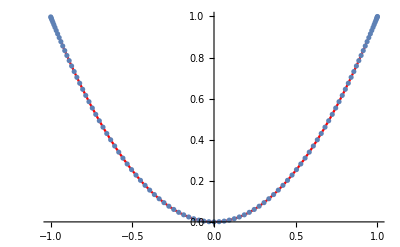

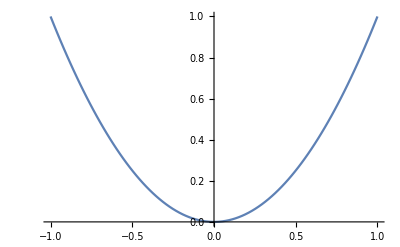

```mathematica
points = data[[All,1]];
fvalues = data[[All,2]];

data1=Table[{points[[i]], fvalues[[i]]},{i,1,Length[points]}];
Show[Plot[1/(1+x^2),{x,-1,1}, PlotStyle->Directive[Red]],(*ListLinePlot[data,Epilog->{PointSize[Small],Point[data1]}] , *)ListPlot[data1,Epilog->{PointSize[Large],Point[data1]}]]
```